## Single mode scalar laser

```mathematica
H={(GL-1) Q/τph + Csp Rsp,α/(2τph) (GL-1),-GL/τe-GL Q/(Γ τph)};
H={(G-1)(1+I α) F/(2 τph)-I ω F,(G-1)(1-I α) Fc/(2 τph)+I ω Fc,1/τe μ-1/τe G - 1/(Γ τph)G F Fc};
Noise=Sqrt[Csp Rsp/2]{{1,I},
{1,-I},
{0,0}};
Diff=Noise.ConjugateTranspose[Noise]//FullSimplify[#,Assumptions->Csp Rsp>0]&;
(*Diff[[3,3]]=Csp Rsp Q;
Diff[[1,3]]=Csp Rsp Q;
Diff[[3,1]]=Csp Rsp Q;*)
vars={F,Fc,G};
linH=Table[D[H[[i]],vars[[j]]],{i,1,3},{j,1,3}];
```

```mathematica
linH//MatrixForm
Diff//MatrixForm
```

(((-1+G) (1+ⅈ α))/(2 τph)-ⅈ ω | 0 | (F (1+ⅈ α))/(2 τph)
0 | ((-1+G) (1-ⅈ α))/(2 τph)+ⅈ ω | (Fc (1-ⅈ α))/(2 τph)
-(Fc G)/(Γ τph) | -(F G)/(Γ τph) | -1/τe-(F Fc)/(Γ τph))

(Csp Rsp | 0 | 0
0 | Csp Rsp | 0
0 | 0 | 0)

```mathematica
linH//MatrixForm
```

(((-1+G) (1+ⅈ α))/(2 τph)-ⅈ ω | 0 | (F (1+ⅈ α))/(2 τph)
0 | ((-1+G) (1-ⅈ α))/(2 τph)+ⅈ ω | (Fc (1-ⅈ α))/(2 τph)
-(Fc G)/(Γ τph) | -(F G)/(Γ τph) | -1/τe-(F Fc)/(Γ τph))

```mathematica
tmp=linH/.{Fc->F,G-> 1+ΔG}/.GLsub/.{1+ΔG-> 1}//FullSimplify;
tmp=linH/.{Fc->F}/.GLsub//FullSimplify;
tmp//MatrixForm
```

(0 | 0 | ((1+ⅈ α) √Γ √(-1+μ))/(2 √τe √τph)
0 | 0 | ((1-ⅈ α) √Γ √(-1+μ))/(2 √τe √τph)
-(√(-1+μ))/(√Γ √τe √τph) | -(√(-1+μ))/(√Γ √τe √τph) | -μ/τe)

```mathematica
Eigenvalues[tmp]//FullSimplify[#,Assumptions->{Csp>0,Rsp>0,α>0,τph>0,τe>0,Γ>0,G>0,F>0,μ>1,w>0}]&
```

{0,-(μ+√((4 τe-4 μ τe+μ^2 τph)/τph))/(2 τe),(-μ+√((4 τe-4 μ τe+μ^2 τph)/τph))/(2 τe)}

```mathematica
matlabsub={τe-> 1,τph-> 1/(2*300),μ->2,Γ->1,α->5,Csp-> 10^-5,Rsp->1};
```

```mathematica
{0,-((μ+Sqrt[(4 τe-4 μ τe+μ^2 τph)/τph])/(2 τe)),(-μ+Sqrt[(4 τe-4 μ τe+μ^2 τph)/τph])/(2 τe)}/.matlabsub//N
```

{0.,-1.-24.4745 ⅈ,-1.+24.4745 ⅈ}

```mathematica
cov=Inverse[tmp-I w*IdentityMatrix[3]].Diff.Inverse[ConjugateTranspose[tmp-I w*IdentityMatrix[3]]];
```

```mathematica
spec=cov[[1,2]]/.{Fc-> F}//FullSimplify[#,Assumptions->{Csp>0,Rsp>0,α>0,τph>0,τe>0,Γ>0,G>0,F>0,μ>1,w>0}]&;
```

```mathematica
(cov[[1,2]]//FullSimplify[#,Assumptions->{Csp>0,Rsp>0,α>0,τph>0,τe>0,Γ>0,G>0,F>0,μ>1,w>0,ΔG>0}]&)
```

(Csp Rsp (-1+μ) (-(1+α^2) (-1+μ)+2 w^2 (1+ⅈ α) τe τph))/(2 w^2 (-2 μ (1+w^2 τe τph)+(1+w^2 τe τph)^2+μ^2 (1+w^2 τph^2)))

```mathematica
Csp*Rsp/4/F^2*(1+α^2)/.GLsub/.matlabsub//N
```

0.039

```mathematica
-2 μ (1+w^2 τe τph)+(1+w^2 τe τph)^2+μ^2 (1+w^2 τph^2)//Expand//CoefficientList[#,w^2]&
```

{1-2 μ+μ^2,2 τe τph-2 μ τe τph+μ^2 τph^2,τe^2 τph^2}

```mathematica
%[[1]]-%[[2]]^2/4/%[[3]]/.matlabsub//N
```

0.00665556

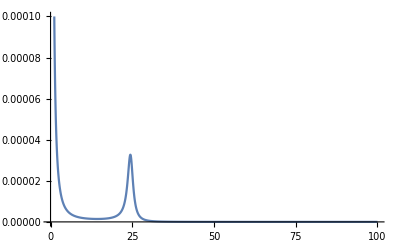

```mathematica
Plot[Abs[spec/.matlabsub],{w,0,100},PlotRange->{Automatic,{0,10^-4}}]
```

```mathematica
SetDirectory["D:\\work\\VCSEL experiments\\Parametr measurement"];
```

```mathematica
Export["file.mat",Table[{w,Abs[spec/.matlabsub]},{w,0,50,0.01}]];
```

Power::infy: Infinite expression 1/0.^2 encountered.

```mathematica
data=Table[Abs[spec/.matlabsub],{w}]
```

```mathematica
(((1+α^2) ΔG (2+(-2+ΔG) μ-I w ΔG τe)+4 w (I+I (-1+ΔG) μ+w ΔG τe) τph-4 w^2 (μ-I w τe) τph^2) ((1+α^2) ΔG (2+(-2+ΔG) μ+I w ΔG τe)+4 w (-I (1+(-1+ΔG) μ)+w ΔG τe) τph-4 w^2 (μ+I w τe) τph^2))//Expand//Collect[#,w]&
```

4 ΔG^2+8 α^2 ΔG^2+4 α^4 ΔG^2-8 ΔG^2 μ-16 α^2 ΔG^2 μ-8 α^4 ΔG^2 μ+4 ΔG^3 μ+8 α^2 ΔG^3 μ+4 α^4 ΔG^3 μ+4 ΔG^2 μ^2+8 α^2 ΔG^2 μ^2+4 α^4 ΔG^2 μ^2-4 ΔG^3 μ^2-8 α^2 ΔG^3 μ^2-4 α^4 ΔG^3 μ^2+ΔG^4 μ^2+2 α^2 ΔG^4 μ^2+α^4 ΔG^4 μ^2+16 w^6 τe^2 τph^4+w^2 (ΔG^4 τe^2+2 α^2 ΔG^4 τe^2+α^4 ΔG^4 τe^2+8 ΔG^2 τe τph+8 α^2 ΔG^2 τe τph-8 ΔG^2 μ τe τph-8 α^2 ΔG^2 μ τe τph+16 τph^2-32 μ τph^2+16 ΔG μ τph^2-16 α^2 ΔG μ τph^2+16 μ^2 τph^2-16 ΔG μ^2 τph^2+16 α^2 ΔG μ^2 τph^2+8 ΔG^2 μ^2 τph^2-8 α^2 ΔG^2 μ^2 τph^2)+w^4 (8 ΔG^2 τe^2 τph^2-8 α^2 ΔG^2 τe^2 τph^2+32 τe τph^3-32 μ τe τph^3+16 μ^2 τph^4)

```mathematica
Inverse[linH-I w]//FullSimplify//MatrixForm
```

((Q^2 α τph)/((-1+GL) Q^2 α+Csp Rsp (2 Q-α) τph^2) | -(2 Q^3 τph)/((-1+GL) Q^2 α+Csp Rsp (2 Q-α) τph^2) | (Q^2 (2 Q-α) τph)/((-1+GL) Q^2 α+Csp Rsp (2 Q-α) τph^2)
-(τph (Q^2 w α+Csp Rsp τph (ⅈ α+2 w τph)))/((-1+GL) Q^2 w α+Csp Rsp w (2 Q-α) τph^2) | (2 τph (Q^2 (1-GL+Q) w+ⅈ Csp Q Rsp τph+Csp Rsp w τph^2))/((-1+GL) Q^2 w α+Csp Rsp w (2 Q-α) τph^2) | (Q^2 (ⅈ (-1+GL) α+w (-2+2 GL-2 Q+α) τph))/((-1+GL) Q^2 w α+Csp Rsp w (2 Q-α) τph^2)
(2 Csp Rsp τph^3)/((-1+GL) Q^2 α+Csp Rsp (2 Q-α) τph^2) | (2 (-1+GL) Q^2 τph-2 Csp Rsp τph^3)/((-1+GL) Q^2 α+Csp Rsp (2 Q-α) τph^2) | -(2 (-1+GL) Q^2 τph)/((-1+GL) Q^2 α+Csp Rsp (2 Q-α) τph^2))

```mathematica
GLsub=Solve[(H/.{Fc-> F})==0,{F,G,ω}][[3]]//FullSimplify;
GLsub
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F→(√Γ √(-1+μ) √τph)/(√τe),G→1,ω→0}

```mathematica
H//MatrixForm
```

((F (-1+G) (1+ⅈ α))/(2 τph)-ⅈ F ω
(Fc (-1+G) (1-ⅈ α))/(2 τph)+ⅈ Fc ω
-G/τe+μ/τe-(F Fc G)/(Γ τph))

```mathematica
{H[[1]]+H[[2]],H[[1]]-H[[2]],H[[3]]}/.{Fc-> F,G->1,ω->0}//FullSimplify//MatrixForm
```

(0
0
(-1+μ)/τe-F^2/(Γ τph))

```mathematica
h={
(G-1)/(2τph)*(Er-α Ei),
(G-1)/(2τph)*(Ei+α Er),
μ/τe-G/τe-G*(Er^2+Ei^2)/(Γ τph)};
σ={
{Sqrt[Csp*Rsp/2]},
{Sqrt[Csp*Rsp/2]},
{0}};
DD=1/2*σ.Transpose[σ];
vars={Er,Ei,G};
-Sum[D[h[[i]]*p[vars[[1]],vars[[2]],vars[[3]]],vars[[i]]],{i,1,3}]+Sum[D[DD[[i,j]]*p[vars[[1]],vars[[2]],vars[[3]]],vars[[i]],vars[[j]]],{i,1,3},{j,1,3}]//FullSimplify
```

1/(4 Γ τe τph)(4 ((Ei^2+Er^2+Γ-G Γ) τe+Γ τph) p[Er,Ei,G]+4 ((Ei^2+Er^2) G τe+Γ (G-μ) τph) p^(0,0,1)[Er,Ei,G]+Γ τe (2 (-1+G) (-(Ei+Er α) p^(0,1,0)[Er,Ei,G]+(-Er+Ei α) p^(1,0,0)[Er,Ei,G])+Csp Rsp τph (p^(0,2,0)[Er,Ei,G]+2 p^(1,1,0)[Er,Ei,G]+p^(2,0,0)[Er,Ei,G])))

```mathematica
DD//MatrixForm
```

((Csp Rsp)/4 | (Csp Rsp)/4 | 0
(Csp Rsp)/4 | (Csp Rsp)/4 | 0
0 | 0 | 0)

```mathematica
FourierTransform[HeavisideTheta[t]*Exp[λ*t],t,w]
```

ⅈ/(√(2 π) (w-ⅈ λ))

```mathematica
InverseFourierTransform[I/(Sqrt[2 π] (w-I λ)),w,t]//FullSimplify
```

-ⅇ^(t λ) HeavisideTheta[-t Sign[Re[λ]]] Sign[Re[λ]]

```mathematica
FourierTransform[HeavisideTheta[t],t,w]
```

ⅈ/(√(2 π) w)+√(π/2) DiracDelta[w]

```mathematica
InverseFourierTransform[Exp[(I λ w-w^2/2)*t],w,x]//FullSimplify
```

(ⅇ^(-(x-t λ)^2/(2 t)))/(√t)

```mathematica
psol=DSolve[p''[x]/2+2*x*p'[x]==λ p[x],p[x],x]//FullSimplify
```

{{p[x]→ⅇ^(-2 x^2) (C[1] HermiteH[-1-λ/2,√2 x]+C[2] Hypergeometric1F1[(2+λ)/4,1/2,2 x^2])}}

```mathematica
(p[x]/.psol/.{λ->0})*(p[x]/.psol/.{λ->1})//FullSimplify//Integrate[#,{x,-Infinity,Infinity}]&
```

Integrate::idiv: Integral of C[2]^2+√(π/2) C[1] C[2] Erf[√2 x]+1/8 π C[1]^2 Erf[√2 x]^2+x^2 C[2] HypergeometricPFQ[{1,1},{3/2,2},-2 x^2]+1/2 √(π/2) x^2 C[1] Erf[√2 x] HypergeometricPFQ[{1,1},{3/2,2},-2 x^2] does not converge on {-∞,∞}.

{∫_(-∞)^∞ 1/16 (4 C[2]+√(2 π) C[1] Erf[√2 x]) (4 C[2]+√(2 π) C[1] Erf[√2 x]+4 x^2 HypergeometricPFQ[{1,1},{3/2,2},-2 x^2])ⅆx}

```mathematica
(p[x]/.psol/.{λ->0})*(p[x]/.psol/.{λ->1})//FullSimplify
```

{1/16 (4 C[2]+√(2 π) C[1] Erf[√2 x]) (4 C[2]+√(2 π) C[1] Erf[√2 x]+4 x^2 HypergeometricPFQ[{1,1},{3/2,2},-2 x^2])}

```mathematica
DSolve[p''[x]+2*x*p'[x]==0,p[x],x]
```

{{p[x]→C[2]+1/2 √(π/2) C[1] Erf[√2 x]}}

```mathematica
InverseLaplaceTransform[1/(s-f),s,t]
```

ⅇ^(f t)

```mathematica
LaplaceTransform
```

```mathematica
DSolve[p''[x]/2+λ p'[x]==0,p[x],x]
```

{{p[x]→-(ⅇ^(-2 x λ) C[1])/(2 λ)+C[2]}}

```mathematica
Integrate[(x+x_0)E^(-((x-t λ)^2/(2 t)))/Sqrt[t],{x,-Infinity,Infinity}]
```

ConditionalExpression[√(2 π),Re[t]≥0]

```mathematica
2z/Sqrt[π]*HypergeometricPFQ[{1/2},{3/2},-z^2]
```

Erf[z]

```mathematica
(*x^3*)
```

```mathematica
psol=DSolve[p''[x]*n/2+p'[x]==λ p[x],p[x],x]//FullSimplify
```

{{p[x]→ⅇ^(-(x (1+√(1+2 n λ)))/n) (C[1]+ⅇ^((2 x √(1+2 n λ))/n) C[2])}}

```mathematica
Integrate[1/3 x ExpIntegralE[2/3,(2 x^3)/n],{x,-Infinity,Infinity}]//FullSimplify
```

(((1/n)^(2/3)+(-1/n)^(5/3) n) π)/(2^(2/3) √3 (-1/n^2)^(2/3) Gamma[-2/3])

```mathematica
Integrate[1/3 x ExpIntegralE[2/3,(2 x^3)/n],{x,-Infinity,Infinity}]
```

```mathematica
Integrate[x*Sqrt[θ/(2π Δ (1 - Exp[-2θ t]))]*Exp[-θ/(2Δ)*(x-x0*Exp[-θ t])^2/(1-Exp[-2θ t])],{x,-Infinity,Infinity},Assumptions->{θ>0&&Δ>0&&t>0&&x0∈Reals}]
```

ⅇ^(-t θ) x0

```mathematica
Integrate[E^(-t θ) x0*x0*E^(-((x0^2 θ)/(2 Δ))),{x0,-Infinity,Infinity}]/Integrate[E^(-((x0^2 θ)/(2 Δ))),{x0,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-t θ) Δ)/θ,Re[θ/Δ]>0]

```mathematica
DSolve[n/2  p''[x]+x p'[x]+p[x]==λ p[x],p[x],x]
```

{{p[x]→ⅇ^(-x^2/n) C[1] HermiteH[-λ,x/(√n)]+ⅇ^(-x^2/n) C[2] Hypergeometric1F1[λ/2,1/2,x^2/n]}}

```mathematica
DSolve[p''[x]+x p'[x]+p[x]==λ p[x],p[x],x]
```

{{p[x]→ⅇ^(-x^2/2) C[1] HermiteH[-λ,x/(√2)]+ⅇ^(-x^2/2) C[2] Hypergeometric1F1[λ/2,1/2,x^2/2]}}

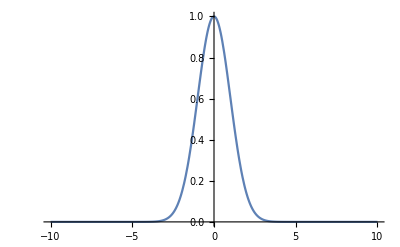

```mathematica
Plot[E^(-(x^2/2)) HermiteH[0,x/Sqrt[2]],{x,-10,10},PlotRange->Full]
```

```mathematica
dusub={p[x]->E^(-(x^2/n)) C[1] HermiteH[-λ,x/Sqrt[n]]};
n/2 D[ p[x]/.dusub,{x,2}]+x D[p[x]/.dusub,x]+(1-λ)p[x]/.dusub//FullSimplify
```

0

```mathematica
dusub2=dusub/.{λ->-1}
```

{p[x]→(2 ⅇ^(-x^2/n) x C[1])/(√n)}

```mathematica
n/2 D[ p[x]/.dusub2,{x,2}]+x D[p[x]/.dusub2,x]+(1+1)p[x]/.dusub2//FullSimplify
```

0

```mathematica
Sqrt[2π] FourierTransform[Exp[λ Abs[t]],t,w]
```

-(2 λ)/(w^2+λ^2)

```mathematica
Integrate[-2λ/(w^2+λ^2),{λ,-Infinity,Infinity}]
```

Integrate::idiv: Integral of -(2 λ)/(w^2+λ^2) does not converge on {-∞,∞}.

∫_(-∞)^∞ -(2 λ)/(w^2+λ^2)ⅆλ

```mathematica
DSolve[{p''[x]+x^3 p'[x]+3x^2 p[x]==0 p[x],p[0]== 1,p'[0]== 0},p[x],x]
```

{{p[x]→ⅇ^(-x^4/4)}}

```mathematica
p[x]=Exp[-x^4/4]*f[x]
```

ⅇ^(-x^4/4) f[x]

```mathematica
D[p[x],{x,2}]+x^3 D[ p[x],x]+3x^2 p[x]-λ p[x]//FullSimplify
```

ⅇ^(-x^4/4) (-λ f[x]-x^3 f'[x]+f''[x])

```mathematica
DSolve[-x^3 f'[x]+f''[x]==0,f[x],x]
```

{{f[x]→C[2]-(x C[1] Gamma[1/4,-x^4/4])/(2 √2 (-x^4)^(1/4))}}

```mathematica
Clear[a]
```

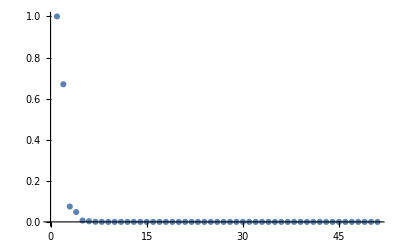

```mathematica
λsub={λ->1.34};
Lst=RecurrenceTable[{a[n+2]==(λ a[n]+a[n-2] (n-2))/(n+1)/(n+2)/.λsub,a[0]== 1,a[1]==0,a[2]== λ/2/.λsub,a[3]==0},a,{n,0,100}];
ListPlot[Lst[[1;;-1;;2]],PlotRange->Full]
```

```mathematica
RecurrenceTable[{a[n+2]==(λ a[n]+a[n-2] (n-2))/(n+1)/(n+2),a[0]== 1,a[1]==0,a[2]== λ/2,a[3]==0},a,{n,0,20}]//FullSimplify
```

{1,0,λ/2,0,λ^2/24,0,1/720 λ (24+λ^2),0,(λ^2 (144+λ^2))/40320,0,(λ (8064+480 λ^2+λ^4))/3628800,0,(λ^2 (111744+1200 λ^2+λ^4))/479001600,0,(λ (10644480+745344 λ^2+2520 λ^4+λ^6))/87178291200,0,(λ^2 (254693376+3366144 λ^2+4704 λ^4+λ^6))/20922789888000,0,(λ (35765452800+2759049216 λ^2+11833344 λ^4+8064 λ^6+λ^8))/6402373705728000,0,(λ^2 (1282744221696+19239690240 λ^2+34864128 λ^4+12960 λ^6+λ^8))/2432902008176640000}

```mathematica
RecurrenceTable[{a[n+2]==(λ a[n]+a[n-2] (n-2))/(n+1)/(n+2),a[0]== 0,a[1]==1,a[2]== 0,a[3]==λ/6},a,{n,0,20}]//FullSimplify
```

{0,1,0,λ/6,0,1/120 (6+λ^2),0,(λ (66+λ^2))/5040,0,(1260+276 λ^2+λ^4)/362880,0,(λ (34524+780 λ^2+λ^4))/39916800,0,(1247400+307764 λ^2+1770 λ^4+λ^6)/6227020800,0,(λ (60490584+1646244 λ^2+3486 λ^4+λ^6))/1307674368000,0,(3405402000+900686304 λ^2+6478344 λ^4+6216 λ^6+λ^8)/355687428096000,0,(λ (250206984720+7617361824 λ^2+20701224 λ^4+10296 λ^6+λ^8))/121645100408832000,0}

```mathematica
DSolve[f''[x]-x^3 f'[x]== -12 f[x],f[x],x]
```

{{f[x]→DifferentialRoot[Function[{y,x},{12 y[x]-x^3 y'[x]+y''[x]==0,y[0]==C[1],y'[0]==C[2]}]][x]}}

```mathematica
NSolve[8064+480 λ^2+λ^4==0,λ]
```

{{λ→0.-4.1753 ⅈ},{λ→0.+4.1753 ⅈ},{λ→0.-21.5074 ⅈ},{λ→0.+21.5074 ⅈ}}

```mathematica
NIntegrate[E^(-(x^4/4)),{x,-Infinity,Infinity}]
```

2.56369

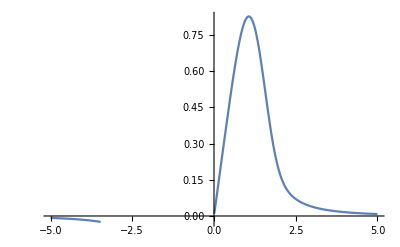

```mathematica
Plot[(E^(-(x^4/4)) ((1-I) x^3 Gamma[1/4]+Sqrt[2] (-x^4)^(3/4) Gamma[1/4,-(x^4/4)]))/(4 x^3),{x,-5,5},PlotRange->Full]
```

```mathematica
DSolve
```

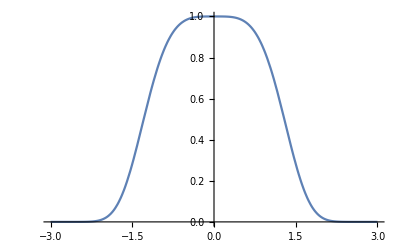

```mathematica
Plot[E^(-(x^4/4)),{x,-3,3}]
```

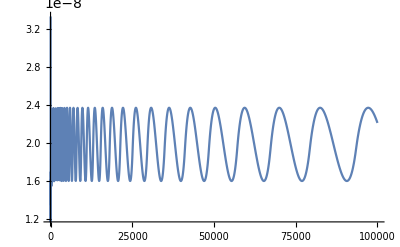

```mathematica
Plot[DifferentialRoot[Function[{y,x},{(0+3 x^2) y[x]+x^3 y'[x]+y''[x]==0,y[0]==1,y'[0]==0}]][x],{x,-1,100000}]
```

```mathematica
NIntegrate[DifferentialRoot[Function[{y,x},{(0+3 x^2) y[x]+x^3 y'[x]+y''[x]==0,y[0]==1,y'[0]==0}]][x]*x,{x,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {8.16907×10^224}. NIntegrate obtained 4.27867155412506×10^55894 and 4.27867155412506×10^55894 for the integral and error estimates.

4.27867155412506×10^55894

```mathematica
NIntegrate[DifferentialRoot[Function[{y,x},{(1+3 x^2) y[x]+x^3 y'[x]+y''[x]==0,y[0]==0,y'[0]==1}]][x]*x,{x,-Infinity,Infinity}]
```

$Aborted

## VCSEL case

```mathematica
ClearAll["Global`*"];
eq1=κ(1+I α)(G+d-1)Fp-(γa+I γp)Fm;
eq2=κ(1+I α)(G-d-1)Fm-(γa+I γp)Fp;
eq3=γ(μ-G)-γ G(Abs[Fp]^2+Abs[Fm]^2)-γ d (Abs[Fp]^2-Abs[Fm]^2);
eq4=-γd d-γ G(Abs[Fp]^2-Abs[Fm]^2)-γ d (Abs[Fp]^2+Abs[Fm]^2);
eqs={eq1,eq2,eq3,eq4};
```

```mathematica
eqNoise={
Sqrt[κ Csp (G+d+T)]*{1, I,0,0},
Sqrt[κ Csp (G-d+T)]*{0,0,1,I},
{0,0,0,0},{0,0,0,0}
};
```

```mathematica
xychange={Fp-> (Fx+I Fy)/Sqrt[2],Fm-> (Fx-I Fy)/Sqrt[2]};
xycM={
{1/Sqrt[2],1/Sqrt[2],0,0},
{1/(Sqrt[2]I),-1/(Sqrt[2]I),0,0},
{0,0,1,0},
{0,0,0,1}};
xyEqs=xycM.eqs/.xychange//FullSimplify;
xyNoise=xycM.eqNoise//FullSimplify;
xyEqs//MatrixForm
```

(-Fx (γa+ⅈ γp)+(ⅈ d Fy+Fx (-1+G)) (1+ⅈ α) κ
d Fx (-ⅈ+α) κ+Fy (γa+ⅈ γp+(-1+G) (1+ⅈ α) κ)
-γ (G-μ+(ⅈ d Fy+Fx G) Conjugate[Fx]+(-ⅈ d Fx+Fy G) Conjugate[Fy])
-d γd-(d Fx+ⅈ Fy G) γ Conjugate[Fx]+(-d Fy+ⅈ Fx G) γ Conjugate[Fy])

```mathematica
xyNoise//MatrixForm
```

((√(Csp (d+G+T) κ))/(√2) | (ⅈ √(Csp (d+G+T) κ))/(√2) | (√(Csp (-d+G+T) κ))/(√2) | (ⅈ √(Csp (-d+G+T) κ))/(√2)
-(ⅈ √(Csp (d+G+T) κ))/(√2) | (√(Csp (d+G+T) κ))/(√2) | (ⅈ √(Csp (-d+G+T) κ))/(√2) | -(√(Csp (-d+G+T) κ))/(√2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
rotEqs=((xyEqs/.{Fy->Fy Exp[I ω t],Fx-> Fx Exp[I ω t]})-{I ω Fx Exp[I ω t],I ω Fy Exp[I ω t],0,0})*{Exp[-I ω t],Exp[-I ω t],1,1}//FullSimplify[#,Assumptions->{ω>0,t>0}]&;
rotNoise=xyNoise;
rotEqs//MatrixForm
```

(-d Fy (-ⅈ+α) κ-Fx (γa+ⅈ (γp-(-1+G) (-ⅈ+α) κ+ω))
d Fx (-ⅈ+α) κ+Fy (γa+ⅈ (γp+(-1+G) (-ⅈ+α) κ-ω))
-γ (G-μ+(ⅈ d Fy+Fx G) Conjugate[Fx]+(-ⅈ d Fx+Fy G) Conjugate[Fy])
-d γd-(d Fx+ⅈ Fy G) γ Conjugate[Fx]+(-d Fy+ⅈ Fx G) γ Conjugate[Fy])

```mathematica
cEqs=({rotEqs[[1]],rotEqs[[1]]//Conjugate,rotEqs[[2]],rotEqs[[2]]//Conjugate,rotEqs[[3]],rotEqs[[4]]}//ComplexExpand[#,{Fx,Fy}]&//FullSimplify[#,Assumptions->{{α,κ,γ,γd,γa,γp,d,G,ω}∈Reals}]&)/.{Conjugate[Fx]->Fxc,Conjugate[Fy]->Fyc};
cNoise={rotNoise[[1]],rotNoise[[1]]//Conjugate,rotNoise[[2]],rotNoise[[2]]//Conjugate,rotNoise[[3]],rotNoise[[4]]}//FullSimplify[#,Assumptions->_∈Reals]&;
cEqs//MatrixForm
```

(-d Fy (-ⅈ+α) κ-Fx (γa+ⅈ (γp-(-1+G) (-ⅈ+α) κ+ω))
-d Fyc (ⅈ+α) κ-Fxc (γa-ⅈ (γp-(-1+G) (ⅈ+α) κ+ω))
d Fx (-ⅈ+α) κ+Fy (γa+ⅈ (γp+(-1+G) (-ⅈ+α) κ-ω))
d Fxc (ⅈ+α) κ+Fyc (γa-ⅈ (γp+(-1+G) (ⅈ+α) κ-ω))
-γ (G+Fxc (ⅈ d Fy+Fx G)+Fyc (-ⅈ d Fx+Fy G)-μ)
Fyc (-d Fy+ⅈ Fx G) γ-Fxc (d Fx+ⅈ Fy G) γ-d γd)

```mathematica
cvars={Fx,Fxc,Fy,Fyc,G,d};
clin=Table[D[cEqs[[i]],cvars[[j]]],{i,1,6},{j,1,6}]//FullSimplify;
clin//MatrixForm
```

(-γa-ⅈ (γp-(-1+G) (-ⅈ+α) κ+ω) | 0 | -d (-ⅈ+α) κ | 0 | Fx (1+ⅈ α) κ | -Fy (-ⅈ+α) κ
0 | -γa+ⅈ (γp-(-1+G) (ⅈ+α) κ+ω) | 0 | -d (ⅈ+α) κ | Fxc (1-ⅈ α) κ | -Fyc (ⅈ+α) κ
d (-ⅈ+α) κ | 0 | γa+ⅈ (γp+(-1+G) (-ⅈ+α) κ-ω) | 0 | Fy (1+ⅈ α) κ | Fx (-ⅈ+α) κ
0 | d (ⅈ+α) κ | 0 | γa-ⅈ (γp+(-1+G) (ⅈ+α) κ-ω) | Fyc (1-ⅈ α) κ | Fxc (ⅈ+α) κ
ⅈ d Fyc γ-Fxc G γ | -(ⅈ d Fy+Fx G) γ | -(ⅈ d Fxc+Fyc G) γ | ⅈ d Fx γ-Fy G γ | -(1+Fx Fxc+Fy Fyc) γ | -ⅈ (Fxc Fy-Fx Fyc) γ
-d Fxc γ+ⅈ Fyc G γ | -(d Fx+ⅈ Fy G) γ | -(d Fyc+ⅈ Fxc G) γ | (-d Fy+ⅈ Fx G) γ | ⅈ (-Fxc Fy γ+Fx Fyc γ) | -(Fx Fxc+Fy Fyc) γ-γd)

```mathematica
(*Consider linear case*)
lPsub={Fy->0,Fyc->0,d->0,Fxc->Fx};
linstateqs={cEqs[[1]]/Fx,cEqs[[2]]/Fx,cEqs[[5]]/γ}/.lPsub//FullSimplify;
linsub=Solve[linstateqs==0,{Fx,G,ω}][[2]];
```

```mathematica
clinlin=clin/.lPsub//FullSimplify;
clinlin[[1;;4,1;;4]]=clinlin[[1;;4,1;;4]]/.linsub//FullSimplify;
clinlin//MatrixForm
lPNoise=cNoise/.lPsub//FullSimplify;
```

(0 | 0 | 0 | 0 | Fx (1+ⅈ α) κ | 0
0 | 0 | 0 | 0 | Fx (1-ⅈ α) κ | 0
0 | 0 | 2 (γa+ⅈ γp) | 0 | 0 | Fx (-ⅈ+α) κ
0 | 0 | 0 | 2 (γa-ⅈ γp) | 0 | Fx (ⅈ+α) κ
-Fx G γ | -Fx G γ | 0 | 0 | -(1+Fx^2) γ | 0
0 | 0 | -ⅈ Fx G γ | ⅈ Fx G γ | 0 | -Fx^2 γ-γd)

```mathematica
lPNoise.ConjugateTranspose[lPNoise]//FullSimplify//MatrixForm
lPDiff=DiagonalMatrix[2Csp κ (G+T)*{1,1,1,1,0,0}];
```

(2 Abs[Csp (G+T) κ] | 0 | 0 | 0 | 0 | 0
0 | 2 Abs[Csp (G+T) κ] | 0 | 0 | 0 | 0
0 | 0 | 2 Abs[Csp (G+T) κ] | 0 | 0 | 0
0 | 0 | 0 | 2 Abs[Csp (G+T) κ] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Inverse[clinlin-I w *IdentityMatrix[6]].lPDiff.Inverse[ConjugateTranspose[clinlin-I w*IdentityMatrix[6]]]//ComplexExpand
```

$Aborted

```mathematica
tmp=clinlin[[{1,2,5},{1,2,5}]];
tmp//MatrixForm
```

(0 | 0 | Fx (1+ⅈ α) κ
0 | 0 | Fx (1-ⅈ α) κ
-Fx G γ | -Fx G γ | -(1+Fx^2) γ)

```mathematica
covtst=Inverse[tmp-I w*IdentityMatrix[3]].DiagonalMatrix[{1,1,0}].Inverse[ConjugateTranspose[tmp-I w*IdentityMatrix[3]]]//Simplify[#,Assumptions->{w>0,α>0,κ>0,G>0,Fx>0,γ>0}]&;
```

```mathematica
Inverse[tmp-I w*IdentityMatrix[3]].DiagonalMatrix[{1,1,0}]//MatrixForm
DiagonalMatrix[{1,1,0}].Inverse[ConjugateTranspose[tmp-I w*IdentityMatrix[3]]]//MatrixForm
```

((-w^2+ⅈ w γ+ⅈ Fx^2 w γ+Fx^2 G γ κ-ⅈ Fx^2 G α γ κ)/(ⅈ w^3+w^2 γ+Fx^2 w^2 γ-2 ⅈ Fx^2 G w γ κ) | (-Fx^2 G γ κ-ⅈ Fx^2 G α γ κ)/(ⅈ w^3+w^2 γ+Fx^2 w^2 γ-2 ⅈ Fx^2 G w γ κ) | 0
(-Fx^2 G γ κ+ⅈ Fx^2 G α γ κ)/(ⅈ w^3+w^2 γ+Fx^2 w^2 γ-2 ⅈ Fx^2 G w γ κ) | (-w^2+ⅈ w γ+ⅈ Fx^2 w γ+Fx^2 G γ κ+ⅈ Fx^2 G α γ κ)/(ⅈ w^3+w^2 γ+Fx^2 w^2 γ-2 ⅈ Fx^2 G w γ κ) | 0
-(ⅈ Fx G w γ)/(ⅈ w^3+w^2 γ+Fx^2 w^2 γ-2 ⅈ Fx^2 G w γ κ) | -(ⅈ Fx G w γ)/(ⅈ w^3+w^2 γ+Fx^2 w^2 γ-2 ⅈ Fx^2 G w γ κ) | 0)

((-Conjugate[w]^2-ⅈ Conjugate[w] Conjugate[γ]-ⅈ Conjugate[Fx]^2 Conjugate[w] Conjugate[γ]+Conjugate[Fx G γ] Conjugate[Fx κ]+ⅈ Conjugate[α] Conjugate[Fx G γ] Conjugate[Fx κ])/(-ⅈ Conjugate[w]^3+Conjugate[w]^2 Conjugate[γ]+Conjugate[Fx]^2 Conjugate[w]^2 Conjugate[γ]+2 ⅈ Conjugate[w] Conjugate[Fx G γ] Conjugate[Fx κ]) | (-Conjugate[Fx G γ] Conjugate[Fx κ]-ⅈ Conjugate[α] Conjugate[Fx G γ] Conjugate[Fx κ])/(-ⅈ Conjugate[w]^3+Conjugate[w]^2 Conjugate[γ]+Conjugate[Fx]^2 Conjugate[w]^2 Conjugate[γ]+2 ⅈ Conjugate[w] Conjugate[Fx G γ] Conjugate[Fx κ]) | (ⅈ Conjugate[w] Conjugate[Fx G γ])/(-ⅈ Conjugate[w]^3+Conjugate[w]^2 Conjugate[γ]+Conjugate[Fx]^2 Conjugate[w]^2 Conjugate[γ]+2 ⅈ Conjugate[w] Conjugate[Fx G γ] Conjugate[Fx κ])
(-Conjugate[Fx G γ] Conjugate[Fx κ]+ⅈ Conjugate[α] Conjugate[Fx G γ] Conjugate[Fx κ])/(-ⅈ Conjugate[w]^3+Conjugate[w]^2 Conjugate[γ]+Conjugate[Fx]^2 Conjugate[w]^2 Conjugate[γ]+2 ⅈ Conjugate[w] Conjugate[Fx G γ] Conjugate[Fx κ]) | (-Conjugate[w]^2-ⅈ Conjugate[w] Conjugate[γ]-ⅈ Conjugate[Fx]^2 Conjugate[w] Conjugate[γ]+Conjugate[Fx G γ] Conjugate[Fx κ]-ⅈ Conjugate[α] Conjugate[Fx G γ] Conjugate[Fx κ])/(-ⅈ Conjugate[w]^3+Conjugate[w]^2 Conjugate[γ]+Conjugate[Fx]^2 Conjugate[w]^2 Conjugate[γ]+2 ⅈ Conjugate[w] Conjugate[Fx G γ] Conjugate[Fx κ]) | (ⅈ Conjugate[w] Conjugate[Fx G γ])/(-ⅈ Conjugate[w]^3+Conjugate[w]^2 Conjugate[γ]+Conjugate[Fx]^2 Conjugate[w]^2 Conjugate[γ]+2 ⅈ Conjugate[w] Conjugate[Fx G γ] Conjugate[Fx κ])
0 | 0 | 0)

```mathematica
covtst//FullSimplify//MatrixForm
```

((w^4+(1+Fx^2)^2 w^2 γ^2-2 Fx^2 G w γ (w+(1+Fx^2) α γ) κ+2 Fx^4 G^2 (1+α^2) γ^2 κ^2)/(w^6+4 Fx^4 G^2 w^2 γ^2 κ^2+w^4 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ)) | (2 Fx^2 G (1+ⅈ α) γ κ (w^2+ⅈ Fx^2 G (ⅈ+α) γ κ))/(w^6+4 Fx^4 G^2 w^2 γ^2 κ^2+w^4 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ)) | (Fx G γ (-w (ⅈ w+γ+Fx^2 γ)+2 Fx^2 G α γ κ))/(w^5+4 Fx^4 G^2 w γ^2 κ^2+w^3 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ))
-(2 Fx^2 G γ κ (ⅈ w^2 (ⅈ+α)+Fx^2 G (1+α^2) γ κ))/(w^6+4 Fx^4 G^2 w^2 γ^2 κ^2+w^4 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ)) | (w^4+(1+Fx^2)^2 w^2 γ^2+2 Fx^2 G w γ (-w+(1+Fx^2) α γ) κ+2 Fx^4 G^2 (1+α^2) γ^2 κ^2)/(w^6+4 Fx^4 G^2 w^2 γ^2 κ^2+w^4 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ)) | -(Fx G γ (w (ⅈ w+γ+Fx^2 γ)+2 Fx^2 G α γ κ))/(w^5+4 Fx^4 G^2 w γ^2 κ^2+w^3 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ))
(Fx G γ (ⅈ w^2-(1+Fx^2) w γ+2 Fx^2 G α γ κ))/(w^5+4 Fx^4 G^2 w γ^2 κ^2+w^3 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ)) | -(Fx G γ (w (-ⅈ w+γ+Fx^2 γ)+2 Fx^2 G α γ κ))/(w^5+4 Fx^4 G^2 w γ^2 κ^2+w^3 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ)) | (2 Abs[Fx G γ]^2)/(w^4+4 Fx^4 G^2 γ^2 κ^2+w^2 γ ((1+Fx^2)^2 γ-4 Fx^2 G κ)))

```mathematica
ConjugateTranspose[tmp-I w*IdentityMatrix[3]]//Simplify[#,Assumptions->{w>0,α>0,κ>0,G>0,Fx>0,γ>0}]&//MatrixForm
```

(ⅈ w | 0 | -Fx G γ
0 | ⅈ w | -Fx G γ
Fx (1-ⅈ α) κ | Fx (1+ⅈ α) κ | ⅈ w-(1+Fx^2) γ)

```mathematica
covtst[[2,1]]//FullSimplify//ApartSquareFree
```

-(1+α^2)/(2 w^2)+(w^2+w^2 α^2+γ^2+2 Fx^2 γ^2+Fx^4 γ^2+α^2 γ^2+2 Fx^2 α^2 γ^2+Fx^4 α^2 γ^2-4 ⅈ Fx^2 G α γ κ-4 Fx^2 G α^2 γ κ)/(2 (w^4+w^2 γ^2+2 Fx^2 w^2 γ^2+Fx^4 w^2 γ^2-4 Fx^2 G w^2 γ κ+4 Fx^4 G^2 γ^2 κ^2))

```mathematica
w^4+w^2 γ^2+2 Fx^2 w^2 γ^2+Fx^4 w^2 γ^2-4 Fx^2 G w^2 γ κ+4 Fx^4 G^2 γ^2 κ^2//FullSimplify[#,ComplexityFunction->f]&
```

w^4+4 Fx^4 G^2 γ^2 κ^2+w^2 γ (γ+2 Fx^2 γ+Fx^4 γ-4 Fx^2 G κ)

```mathematica
covtst[[1,2]]//ApartSquareFree
```

-(1+α^2)/(2 w^2)+(w^2+w^2 α^2+γ^2+2 Fx^2 γ^2+Fx^4 γ^2+α^2 γ^2+2 Fx^2 α^2 γ^2+Fx^4 α^2 γ^2+4 ⅈ Fx^2 G α γ κ-4 Fx^2 G α^2 γ κ)/(2 (w^4+w^2 γ^2+2 Fx^2 w^2 γ^2+Fx^4 w^2 γ^2-4 Fx^2 G w^2 γ κ+4 Fx^4 G^2 γ^2 κ^2))

```mathematica
DiagonalMatrix[{1,1,0}]
```

{{1,0,0},{0,1,0},{0,0,0}}

```mathematica
Eigenvalues[clinlin[[{1,2,5},{1,2,5}]]]//FullSimplify//MatrixForm
```

(0
1/2 (-(1+Fx^2) γ-√γ √((1+Fx^2)^2 γ-8 Fx^2 G κ))
1/2 (-(1+Fx^2) γ+√γ √((1+Fx^2)^2 γ-8 Fx^2 G κ)))

```mathematica
S=Eigenvectors[clinlin[[{1,2,5},{1,2,5}]]]//Transpose;
S.ConjugateTranspose[S]//FullSimplify//MatrixForm
```

(1+((-ⅈ+α) Conjugate[Fx] (ⅈ+Conjugate[α]) Conjugate[κ] (Abs[γ] (1+Fx^2+Abs[Fx]^4+Conjugate[Fx]^2)+√((1+Fx^2)^2 γ-8 Fx^2 G κ) Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]))/(Fx G Abs[γ] ((1+Conjugate[Fx]^2)^2 Conjugate[γ]-Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]^2)) | -1+(Conjugate[κ] (Abs[Fx^6 γ]+Fx Conjugate[Fx] (Abs[γ] (1+Fx^2+Conjugate[Fx]^2)+√((1+Fx^2)^2 γ-8 Fx^2 G κ) Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)])) (-1+Abs[α]^2-2 ⅈ Re[α]))/(Fx^2 G Abs[γ] (-(1+Conjugate[Fx]^2)^2 Conjugate[γ]+Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]^2)) | -(ⅈ (1+Fx^2) (-ⅈ+α))/(2 Fx G)
-1-(Conjugate[κ] (Abs[Fx^6 γ]+Fx Conjugate[Fx] (Abs[γ] (1+Fx^2+Conjugate[Fx]^2)+√((1+Fx^2)^2 γ-8 Fx^2 G κ) Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)])) (-1+Abs[α]^2+2 ⅈ Re[α]))/(Fx^2 G Abs[γ] ((1+Conjugate[Fx]^2)^2 Conjugate[γ]-Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]^2)) | 1-((ⅈ+α) Conjugate[Fx] (-ⅈ+Conjugate[α]) Conjugate[κ] (Abs[γ] (1+Fx^2+Abs[Fx]^4+Conjugate[Fx]^2)+√((1+Fx^2)^2 γ-8 Fx^2 G κ) Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]))/(Fx G Abs[γ] (-(1+Conjugate[Fx]^2)^2 Conjugate[γ]+Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]^2)) | (ⅈ (1+Fx^2) (ⅈ+α))/(2 Fx G)
-(4 Conjugate[Fx] (1+Conjugate[Fx]^2) Conjugate[1/(√γ)] Conjugate[√γ] Conjugate[κ+ⅈ α κ])/((1+Conjugate[Fx]^2)^2 Conjugate[√γ]^2-Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]^2) | -(4 ⅈ Conjugate[Fx] (1+Conjugate[Fx]^2) (-ⅈ+Conjugate[α]) Conjugate[1/(√γ)] Conjugate[√γ] Conjugate[κ])/((1+Conjugate[Fx]^2)^2 Conjugate[√γ]^2-Conjugate[√((1+Fx^2)^2 γ-8 Fx^2 G κ)]^2) | 2)

```mathematica
Inverse[clinlin-I w *IdentityMatrix[6]/.{γa->0,γp-> 0}]//Simplify//MatrixForm
```

((ⅈ w^2+(1+Fx^2) w γ-Fx^2 G (ⅈ+α) γ κ)/(w (w^2-ⅈ (1+Fx^2) w γ-2 Fx^2 G γ κ)) | -(Fx^2 G (-ⅈ+α) γ κ)/(w (w^2-ⅈ (1+Fx^2) w γ-2 Fx^2 G γ κ)) | 0 | 0 | -(ⅈ Fx (-ⅈ+α) κ)/(-w^2+ⅈ (1+Fx^2) w γ+2 Fx^2 G γ κ) | 0
(Fx^2 G (ⅈ+α) γ κ)/(w (w^2-ⅈ (1+Fx^2) w γ-2 Fx^2 G γ κ)) | (ⅈ w^2+(1+Fx^2) w γ+Fx^2 G (-ⅈ+α) γ κ)/(w (w^2-ⅈ (1+Fx^2) w γ-2 Fx^2 G γ κ)) | 0 | 0 | (ⅈ Fx (ⅈ+α) κ)/(-w^2+ⅈ (1+Fx^2) w γ+2 Fx^2 G γ κ) | 0
0 | 0 | (ⅈ w^2+w (Fx^2 γ+γd)-Fx^2 G (ⅈ+α) γ κ)/(w (w^2-ⅈ w (Fx^2 γ+γd)-2 Fx^2 G γ κ)) | (Fx^2 G (-ⅈ+α) γ κ)/(w (w^2-ⅈ w (Fx^2 γ+γd)-2 Fx^2 G γ κ)) | 0 | -(Fx (-ⅈ+α) κ)/(-w^2+ⅈ w (Fx^2 γ+γd)+2 Fx^2 G γ κ)
0 | 0 | -(Fx^2 G (ⅈ+α) γ κ)/(w (w^2-ⅈ w (Fx^2 γ+γd)-2 Fx^2 G γ κ)) | (ⅈ w^2+w (Fx^2 γ+γd)+Fx^2 G (-ⅈ+α) γ κ)/(w (w^2-ⅈ w (Fx^2 γ+γd)-2 Fx^2 G γ κ)) | 0 | -(Fx (ⅈ+α) κ)/(-w^2+ⅈ w (Fx^2 γ+γd)+2 Fx^2 G γ κ)
(Fx G γ)/(-w^2+ⅈ (1+Fx^2) w γ+2 Fx^2 G γ κ) | (Fx G γ)/(-w^2+ⅈ (1+Fx^2) w γ+2 Fx^2 G γ κ) | 0 | 0 | (ⅈ w)/(w^2-ⅈ (1+Fx^2) w γ-2 Fx^2 G γ κ) | 0
0 | 0 | (ⅈ Fx G γ)/(-w^2+ⅈ w (Fx^2 γ+γd)+2 Fx^2 G γ κ) | -(ⅈ Fx G γ)/(-w^2+ⅈ w (Fx^2 γ+γd)+2 Fx^2 G γ κ) | 0 | (ⅈ w)/(w^2-ⅈ w (Fx^2 γ+γd)-2 Fx^2 G γ κ))

```mathematica
Inverse[{{a,0},{0,b}}-I w *IdentityMatrix[2]]//FullSimplify//MatrixForm
```

(1/(a-ⅈ w) | 0
0 | 1/(b-ⅈ w))

```mathematica
M={{1/(a-I w),0},{0,1/(b-I w)}};
M.{{α,β},{γ,δ}}.Conjugate[M]/.{a-> ar+I ai,b-> br+I bi}//ComplexExpand//FullSimplify//MatrixForm
```

(α/(ar^2+(ai-w)^2) | β/((ai-ⅈ ar-w) (bi+ⅈ br-w))
γ/((ai+ⅈ ar-w) (bi-ⅈ br-w)) | δ/(br^2+(bi-w)^2))